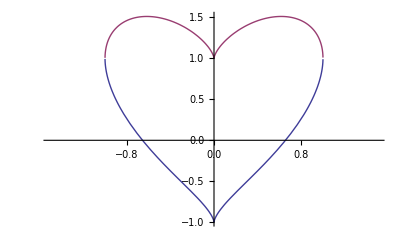

```mathematica
Plot[{(x^2)^(1/3)-√(1-x^2),(x^2)^(1/3)+√(1-x^2)},{x,-1.5,1.5}]
```

```mathematica
Solve[x^2+(y-(x^2)^(1/3))^2==1,y]
```

{{y→(x^2)^(1/3)-√(1-x^2)},{y→(x^2)^(1/3)+√(1-x^2)}}

```mathematica
Animate[ContourPlot3D[(x^2+9/4y^2+z^2-1)^3-x^2z^3-9/(80)y^2z^3==0,{x,-1.5*k,1.5*k},{y,-1.5*k,1.5*k},{z,-1.5*k,1.5*k}],{k,1,1.7,.01},AnimationDirection->ForwardBackward,AnimationRate->.5,AnimationRepetitions->4]
```

```mathematica
Export["Happy Valentine's Day.flv",%]
```

Happy Valentine's Day.flv

```mathematica
Plot3D[Exp[-x^2-0.5*y^2]*Cos[4 x]+Exp[-3 ((x+0.5)^2+0.5 y^2)],{x,-3,3},{y,-5,5},PlotRange->{-0.001,0.001},PlotPoints->40]
```

-Graphics3D-

```mathematica
With[{p:=Random[],
r=RotateLeft},
Graphics3D[Table[{RGBColor[p,.2,.2],Cuboid[l=r[{z,p,p},a],l+r[p/8 {Sign[z-.5],p,p},a]]}, {z,{0,1}},{a,0,2},{6!}]]]
```

-Graphics3D-